```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
Get[NotebookDirectory[]<>"QBMMlibpub.wl"];
Get[NotebookDirectory[]<>"TimeSteppers.wl"];
```

```mathematica
?QBMMlib`*
```

```mathematica
(* Input parameters *)
model="nonlinear";
If[model=="linear",
	Ca=1/2;γ=1;Rey=Infinity;
	Cp0=1;
	Cp[t_]:=Cp0;
	Toneperiod=3.4 (1/Cp0)^0.75;
	(*myeqn=rdd+rd+(r-ro)+Cp[t]==0;*)
	myeqn=rdd+rd+(r-ro)==0;
];
If[model=="nonlinear",
	Ca=1/2;γ=1.4;
	(*Cp0=0.9;*)
	Cp0=1;
	Toneperiod=3.4  (1/Cp0)^0.75;
	Cp[t_]:=1(* Cp0*);
	(*Cp[t_]:=If[t<Toneperiod,Cp0 Sin[2 Pi t/Toneperiod]+1,1];*)
	myeqn=r rdd+(3/2)rd^2==(ro/r)^(3 γ)-Cp[ttt];
];

Nperiod=1;
T=Nperiod Toneperiod;

dt=1.  10^-5;dt0=dt;
dtmin=dt;dtmax=10000dt;
tol=12 10^-6;

μRd=0;σRd=Sqrt[0.05];
𝒟v=NormalDistribution[μRd,σRd];	

dimensions=3;
If[dimensions==2,
	nro=1;
	Ros={1};wRos={1};
	myvars={r,rd};
	myidx={i1,i2};
	{coefs,exs}=getterms[myeqn,myvars,rdd,myidx];
	μR=1.;σR=0.1;
	𝒟r=LogNormalDistribution[Log[μR],σR];
	RRdPDF=ProductDistribution[𝒟r,𝒟v];
	ro=μR;
	momRRd[i_,j_,k_]:=Moment[RRdPDF,{i,j}];
];
If[dimensions==3,
	μRo=1.;σRo=0.1;
	nro=1;
	𝒟ro=LogNormalDistribution[Log[μRo],σRo];
	myvars={r,rd,ro};
	myidx={i1,i2,i3};
	{coefs,exps}=TransportTerms[myeqn,myvars,rdd,myidx];	
	momRo[i_]:=Moment[𝒟ro,i];
	momRos=Table[momRo[i],{i,0,2nro-1}];
	{Ros,wRos}=wheeler[momRos];
	Ros={1};wRos={1};
	(*Ros={0.60462699316458046,0.95776038990257417,1.5171419318631691};
	wRos={1.9470467441388959 10^-6,2.2291939736135009,1.0320276128853133 10^-4};*)
	If[Min[Ros]<0,Print["Negative Ro!"];Abort[];];	
	Do[
		μR=Ros[[i]];σR=0.1;
		𝒟r[i]=LogNormalDistribution[Log[μR],σR];
		(*𝒟r[i]=NormalDistribution[μR,σR];*)
		(*RRdPDF[i]=ProductDistribution[𝒟r[i],𝒟v];*)
		RRdPDF[i]=BinormalDistribution[{μR,μRd},{σR,σRd},0.1];
	,{i,nro}];
	momRRd[i_,j_,k_]:=Moment[RRdPDF[k+1],{i,j}];
	RRdRoPDF=ProductDistribution[𝒟r,𝒟v,𝒟ro];
];

method="CQMOM";(*"CQMOM" or "CHyQMOM"*)
nr=2;
nrd=3;
If[dimensions==2,myn={nr,nrd}];
If[dimensions==3,myn={nr,nrd,nro}];

numperm=2;
If[method=="CHYQMOM"&&nr==3,qmax=0.3];

ks=MomentIndex[myn,method,numperm];
ksp={{3,0,0},{2,1,0},{3,2,0},{3(1-γ),0,3γ}};
```

```mathematica
ks
```

{{0,0,0},{0,1,0},{0,2,0},{0,3,0},{0,4,0},{0,5,0},{1,0,0},{1,1,0},{1,2,0},{1,3,0},{1,4,0},{1,5,0},{2,0,0},{3,0,0},{2,1,0},{3,1,0},{2,2,0},{3,2,0}}

```mathematica
(* 
For cqmom12p: 
	w[l][j,k]
	l = 1,nro 
	j = 1,nr
	k = 1,nrd

	xi[[1]][l] .. length = nr?
	xi[[2]][l][i]
	i = 1,nr; each component length nrd

For cqmom21p: 
	w[l][j,k]
	l = 1,nro 
	j = 1,nrd
	k = 1,nr

	xi[[1]][l] .. length = nrd?
	xi[[2]][l][i]
	i = 1,nrd; each component length nr
*)
```

```mathematica
(* need to load oldCQMOM for these *)
moms=Table[momRRd[ks[[i,1]],ks[[i,2]],ks[[i,3]]],{i,Length[ks]}];
{w,xi}=MomentInvert[moms,ks,Method->"CQMOM",Permutation->12];
Table[w[1][j,k],{j,1,nr},{k,1,nrd}];
xi[[1]][1];(* these are in direction 1 *)
Table[xi[[2]][1][i],{i,1,nr}]; (* these are in direction 2 *)
pts1=Flatten[Table[Thread[{xi[[1]][1][[i]],xi[[2]][1][i]}],{i,nr}],1];
wgt1=Flatten[Table[w[1][j,k],{j,1,nr},{k,1,nrd}]];
pts1x=pts1[[All,1]];
pts1y=pts1[[All,2]];
```

```mathematica
moms=Table[momRRd[ks[[i,1]],ks[[i,2]],ks[[i,3]]],{i,Length[ks]}];
{w,xi}=MomentInvert[moms,ks,Method->"CQMOM",Permutation->21];
Table[w[1][j,k],{j,1,nrd},{k,1,nr}]
xi[[1]][1] ;(* these are in direction 2 *)
Table[xi[[2]][1][i],{i,1,nrd}] ;(*these are in direction 1 *)
pts2=Flatten[Table[Thread[{xi[[2]][1][i],xi[[1]][1][[i]]}],{i,nrd}],1]
wgt2=Flatten[Table[w[1][j,k],{j,nrd},{k,nr}]];
pts2x=pts2[[All,1]];
pts2y=pts2[[All,2]];
```

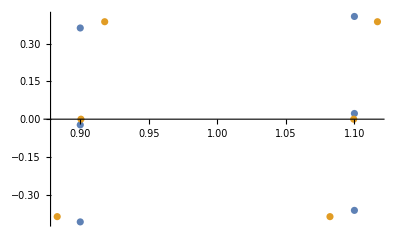

```mathematica
ListPlot[{pts1,pts2}]
```

```mathematica
moms={1,1.0000500012500209,0.0000000000000000,1.0002000200013337,2.5000000000000009 10^-3,0.0000000000000000};
{w,xi}=CHYQMOM[moms,ks];
rhs=Table[frhs3[w,xi,0.1,ks[[i]]],{i,Length[ks]}]
(*CHYQMOM[moms,ks,MaxSkewness->20]*)
```

```mathematica
frhs[w_,xi_,tin_,indx_]:=Module[
	{rhs,rule,myexps,mycoefs},
	rule=Flatten[{Table[myidx[[i]]->indx[[i]],{i,dimensions}],ttt->tin}];
	myexps=Table[exps[[i]]/.rule,{i,Length[exps]}];
	mycoefs=Table[coefs[[i]]/.rule,{i,Length[coefs]}];
	rhs=Sum[
			mycoefs[[i]]pow[Ros[[indx[[3]]+1]],myexps[[i,3]]-indx[[3]]]
			Quadrature2[w,xi,{myexps[[i,1]],myexps[[i,2]],1+indx[[3]]}]
		,{i,Length[coefs]}];
	Return[rhs,Module];
];

myrhs[moms_,t_]:=Module[{},
	If[method=="CHYQMOM",
		{w,xi}=MomentInvert[moms,ks,Method->method];
		rhs=Table[frhs[w,xi,t,ks[[i]]],{i,Length[ks]}];
		momout=Project[w,xi,ks];
	];
	If[method=="CQMOM",
		If[numperm==2,	
			{w,xi}=MomentInvert[moms,ks,Method->"CQMOM",Permutation->12];
			rhs1=Table[frhs[w,xi,t,ks[[i]]],{i,Length[ks]}];
			momout1=Project[w,xi,ks];
			
			{w2,xi2}=MomentInvert[moms,ks,Method->"CQMOM",Permutation->21];
			rhs2=Table[frhs[w2,xi2,t,ks[[i]]],{i,Length[ks]}];
			momout2=Project[w2,xi2,ks];

			momout=(momout1+momout2)/2;
			rhs=(rhs1+rhs2)/2;
			(*Abort[];*)
		,
			{w,xi}=MomentInvert[moms,ks,Method->"CQMOM",Permutation->12];
			rhs=Table[frhs[w,xi,t,ks[[i]]],{i,Length[ks]}];
			momout=Project[w,xi,ks];
			Abort[];
		];
	];
	Return[{momout,rhs},Module];
];
```

```mathematica
(* ic: conditioned moments for each Subscript[R, o,l] *)
moms=Table[momRRd[ks[[i,1]],ks[[i,2]],ks[[i,3]]],{i,Length[ks]}];

sol={};ts={};dets={};abscissa={};fullmoms={};
t=0;dt=dt0;
Monitor[While[t≤T,
	{moms,mome,e}=RK23[moms,myrhs,t,dt];
	(*If[method=="CHYQMOM",AppendTo[abscissa,Table[Thread[{xix[j],xiy[j]}],{j,nro}]]];
	If[method=="CQMOM",AppendTo[abscissa,Table[Flatten[Table[Thread[{xis[j][i],xi[j][[i]]}],{i,nrd}],1],{j,nro}]]];*)
	AppendTo[sol,moms];
	AppendTo[ts,t];

	mominv1[moms_,i_,j_,k_]:=moms[[Position[ks,{i,j,k}][[1,1]]]];

	momtot[i_,j_,k_]:=Sum[wRos[[l+1]]Ros[[l+1]]^k mominv1[moms,i,j,l],{l,0,nro-1}];
	fullmom=Table[momtot[ks[[i,1]],ks[[i,2]],ks[[i,3]]],{i,Length[ks]}];
	momtot[i_,j_,k_]:=Sum[wRos[[l+1]]Ros[[l+1]]^k mominv1[mome,i,j,l],{l,0,nro-1}];
	fullmome=Table[momtot[ks[[i,1]],ks[[i,2]],ks[[i,3]]],{i,Length[ks]}];

	e=Norm[fullmom-fullmome]/Norm[fullmom];
	AppendTo[fullmoms,fullmom];

	t=t+dt;
	dt=dt Min[Max[Sqrt[tol/(2 e)],0.3],2.];
dt=Min[Max[0.9 dt,dtmin],dtmax];

If[Norm[moms]>10^8,Print["Crash ",100 t/T];Break[]];
];
,TableForm[{{"Time",100t/T},{"δt",dt/dt0},{"Moments",Max[Abs[moms]]}}]
]//AbsoluteTiming
Length[ts]
```

{9.68394,Null}

204

```mathematica
moms
```

{1,0,0.05,0,1,0.00223607,0.05,0.00033541,1.01,1.03}

```mathematica
rhs-{0.,0.0835267187574682,-0.019518661365676718,0.012069870990846998,6.938893903907228*^-18,0.08836651359886444,-0.01982271488033641,0.007901441686294332,0.004472135954999609,0.013416407864998786}
```

{0.,0.,1.38778×10^-17,2.77556×10^-17,0.,2.22045×10^-16,1.38778×10^-17,0.,0.,0.}

```mathematica
w[1]
xi[[1]][1]
xi[[2]][1]
(*w2[1]
xi2[[1]][1]
xi2[[2]][1]*)
```

{0.249746,0.250254,0.249746,0.250254}

{1.1,1.1,0.9,0.9}

{0.245073,-0.1999,-0.245073,0.1999}

```mathematica
moms-momout
```

{0.,-3.46945×10^-18,0.,-1.30104×10^-18,0.,-1.12757×10^-17,-6.93889×10^-18,0.000111803,2.22045×10^-16,0.,-1.21431×10^-17,0.0000223607}

```mathematica
momout
```

{1.,1.56125×10^-16,0.05,3.28581×10^-17,0.0075,1.15684×10^-17,1.,0.00223607,0.05,0.00033541,0.0075,0.0000838525,1.01,1.03}

```mathematica
rhs
```

{0.,0.0835267,-0.0195187,-0.0101983,-0.00565232,-0.00272354,1.56125×10^-16,0.0883665,-0.0198227,-0.00924502,-0.00594681,-0.00321052,0.00447214,0.0134164}

```mathematica
w[1]
xi[[1]][1]
xi[[2]][1]
```

{0.0831005,0.0836011,0.333298,0.0831005,0.0836011,0.333298}

{1.1,1.1,1.1,0.9,0.9,0.9}

{0.408215,-0.362421,0.0226712,-0.408215,0.362421,-0.0226712}

```mathematica
myn=100;
plottingfac=1;
myts=Table[ts[[i]],{i,1,Length[abscissa],Floor[Length[abscissa]/myn]}];
Do[myabscissa[j]=Table[abscissa[[i,j]],{i,1,Length[abscissa],Floor[Length[abscissa]/N[myn]]}],{j,nro}];
Do[
	xdat[j]=myabscissa[j][[All,All,1]];
	ydat[j]=myabscissa[j][[All,All,2]];
	xmax[j]=If[Max[xdat[j]]>0,1.2 Max[xdat[j]],0.8 Max[xdat[j]]];
	xmin[j]=If[Min[xdat[j]]<0,1.2 Min[xdat[j]],0.8 Min[xdat[j]]];
	ymax[j]=If[Max[ydat[j]]>0,1.2 Max[ydat[j]],0.8 Max[xdat[j]]];
	ymin[j]=If[Min[ydat[j]]<0,1.2Min[ydat[j]],0.8 Min[ydat[j]]];
,{j,nro}];
xminF=Min[Table[xmin[j],{j,nro}]];
xmaxF=Max[Table[xmax[j],{j,nro}]];
yminF=Min[Table[ymin[j],{j,nro}]];
ymaxF=Max[Table[ymax[j],{j,nro}]];

dat3d=Table[Flatten[Table[Table[Flatten[{Ros[[j]],myabscissa[j][[k,i]]},1],{i,Length[myabscissa[j][[k]]]}],{j,nro}],1],{k,Length[myabscissa[1]]}];
```

```mathematica
ListAnimate[ParallelTable[
ListPlot[
	Table[myabscissa[j][[i]],{j,nro}],PlotRange->{{xminF//Re,xmaxF//Re},{yminF//Re,ymaxF//Re}},AxesLabel->{"R","V"}]
,{i,1,Length[myabscissa[1]]/plottingfac}]]
```

```mathematica
anim=ListAnimate[
	ParallelTable[
		ListPointPlot3D[dat3d[[i]],PlotRange->{{0.9Min[Ros],1.1Max[Ros]},{xminF//Re,xmaxF//Re},{yminF//Re,ymaxF//Re}},
			AxesLabel->{"Ro","R","V"}]
	,{i,Length[dat3d]/plottingfac}]
]
(*Export["~/Desktop/anim2.avi",anim,AnimationRunTime->6];*)
```

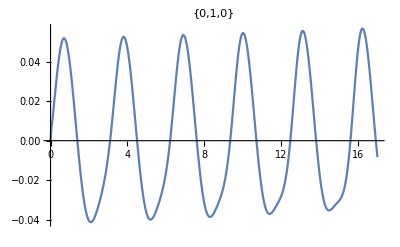
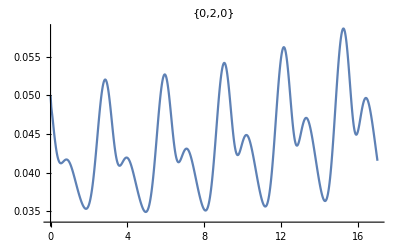
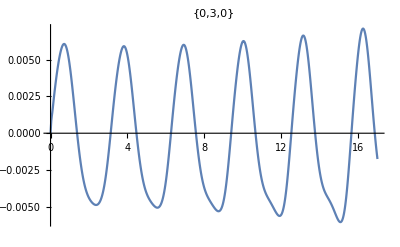
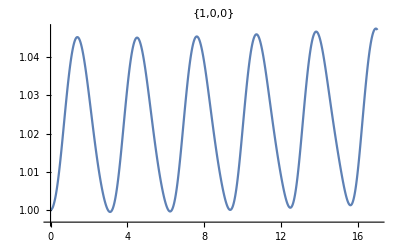
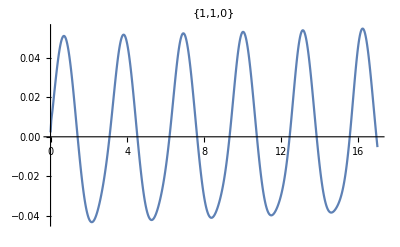
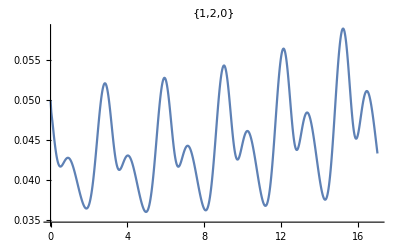
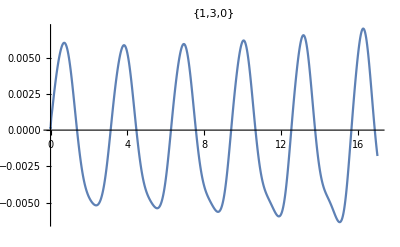
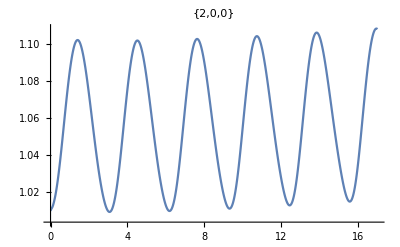

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[Thread[{ts,fullmoms[[All,i]]}],Joined->True,PlotRange->All,PlotLabel->ks[[i]]]]
]
,{i,1,Length[moms]}]
plots
```

```mathematica
(* Verify with Monte Carlo *)
If[
	dimensions==3,
	NcasesRRd=50;
	cases=RandomVariate[RRdRoPDF,Ncases];

	NcasesRo=50;
	casesRo=RandomVariate[𝒟ro,NcasesRo]//Sort;
	Do[casesRRd[i]=RandomVariate[ProductDistribution[LogNormalDistribution[Log[casesRo[[i]]],σR],𝒟v],NcasesRRd],{i,NcasesRo}];
	cases=Flatten[Table[{casesRRd[kk][[i,1]],casesRRd[kk][[i,2]],casesRo[[kk]]},{i,NcasesRRd},{kk,NcasesRo}],1];
	Ncases=Length[cases];
,
	Ncases=3000;
	cases=RandomVariate[RRdPDF,Ncases];
	cases=Table[{cases[[i,1]],cases[[i,2]],ro},{i,Ncases}];
];

Clear[t];
If[model=="linear",
	β=2/Rey;ω2= 2 γ Ca;
	myr=ParallelTable[
	r[t]/.(NDSolve[
{r''[t] == -2 β r'[t]-ω2 r[t]-Cp[t],r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,Ncases}];
];
If[model=="nonlinear",
	myr=ParallelTable[
r[t]/.(NDSolve[
{r[t]r''[t]+3/2 r'[t]^2 ==(cases[[i,3]]/r[t])^(3 γ)-Cp[t],r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,Ncases}];
];
mydr=ParallelTable[D[myr[[i]],t],{i,Ncases}];

Nt=100;ts2=Table[i,{i,0,T,T/Nt}];
ts2=myts;Nt=Length[ts2];
P=Table[
	Table[
	{
	myr[[j]]/.{t->ts2[[i]]},
	mydr[[j]]/.{t->ts2[[i]]},
	cases[[j,3]]
	}
	,{j,Ncases}]
,{i,Nt}];

mcmoms=ParallelTable[Table[{ts2[[i]],Moment[P[[i]],ks[[j,1;;3]]]},{i,Nt}],{j,Length[ks]}];
mcmomssp=ParallelTable[Table[{ts2[[i]],Moment[P[[i]],ksp[[j,1;;3]]]},{i,Nt}],{j,Length[ksp]}];
```

```mathematica
plts=ParallelTable[
Show[
DensityHistogram[P[[i]],PlotRange->{{xmin,xmax},{ymin,ymax},All}],
ListPlot[myabscissa[[i]],PlotStyle->Red,PlotRange->{{xmin,xmax},{ymin,ymax}}]]
,{i,1,Length[P]/1}];
vid=ListAnimate[plts]
```

```mathematica
(*Export["~/Desktop/movie.avi",vid]*)
```

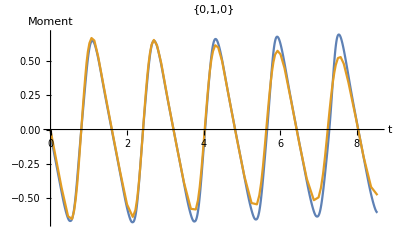
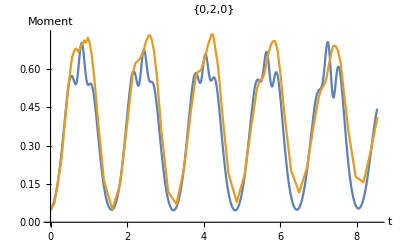
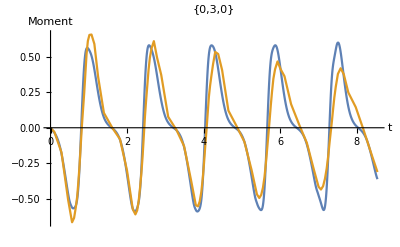
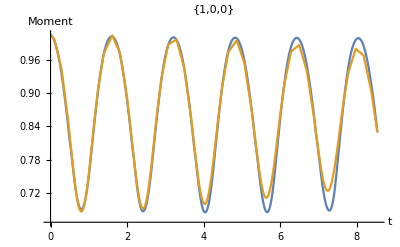
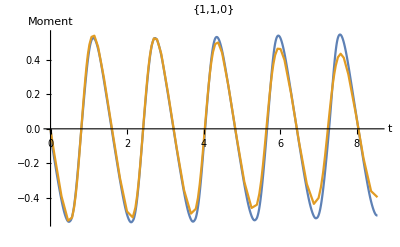
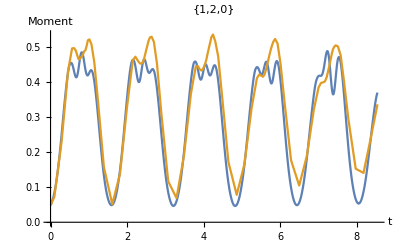
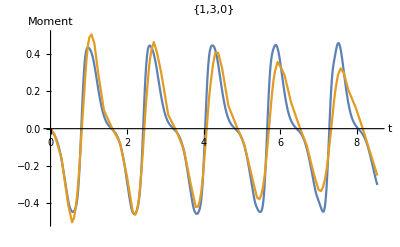
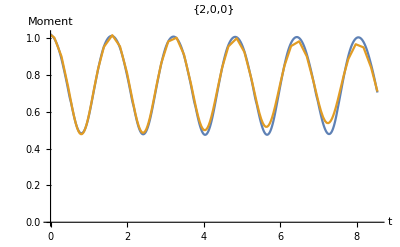

{}

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[{Thread[{ts,fullmoms[[All,i]]}],mcmoms[[i]]},Joined->True,PlotRange->All,PlotLabel->ks[[i]],AxesLabel->{"t","Moment"}]]
]
,{i,1,Length[moms]}]
plots

plots={};
Do[
AppendTo[plots,ListPlot[{Thread[{ts,spsol[[All,i]]}],mcmomssp[[i]]},Joined->True,PlotRange->All,PlotLabel->ksp[[i]],AxesLabel->{"t","Moment"}]]
,{i,1,Length[momsp]}]
plots
```